Set::wrsym: Symbol GoldenRatio is Protected.

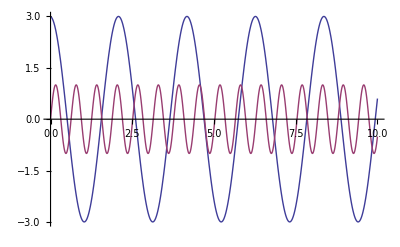

```mathematica
a0 = 1; f0 = 10; GoldenRatio0 = 0;
A = 3; f = 3; GoldenRatio = 0;
Plot[{A Sin[f t + GoldenRatio], a0 Sin[f0 t + GoldenRatio0]}, {t,0,10}(*,PlotRange -> 2*)]
```

```mathematica
Manipulate[
a0 = 1; f0 = 10; GoldenRatio0 = 0;
(*A = 3; f = 3; GoldenRatio = 0;*)
Plot[{A Sin[f t + GoldenRatio], a0 Sin[f0 t + GoldenRatio0]}, {t,0,10},PlotRange -> 2],
{{A, a0, "amplitude"},0,2,Appearance -> "Labeled"}, 
{{f,f0, "frequency"}, 0,10, Appearance -> "Labeled"},
{{GoldenRatio,GoldenRatio0, "instrinsic phase"},0,2 Pi, Appearance -> "Labeled"}]
```